{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r},{q,q,q},{q,p,p},{q,r,r},{p,q,q},{p,p,p},{p,r,r},{r,q,q},{r,p,p},{r,r,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b}},{r}}

True

False

{{a,b,p,q,r},{{q,a,a,p},{q,a,b,p},{q,a,p,p},{q,a,q,p},{q,a,r,p},{q,b,a,r},{q,b,b,r},{q,b,p,r},{q,b,q,r},{q,b,r,r},{p,a,a,r},{p,a,b,r},{p,a,p,r},{p,a,q,r},{p,a,r,r},{p,b,a,q},{p,b,b,q},{p,b,p,q},{p,b,q,q},{p,b,r,q},{r,a,a,r},{r,a,b,r},{r,a,p,r},{r,a,q,r},{r,a,r,r},{r,b,a,r},{r,b,b,r},{r,b,p,r},{r,b,q,r},{r,b,r,r},{q,q,a,q},{q,q,b,q},{q,q,p,q},{q,q,q,q},{q,q,r,q},{q,p,a,p},{q,p,b,p},{q,p,p,p},{q,p,q,p},{q,p,r,p},{q,r,a,r},{q,r,b,r},{q,r,p,r},{q,r,q,r},{q,r,r,r},{p,q,a,q},{p,q,b,q},{p,q,p,q},{p,q,q,q},{p,q,r,q},{p,p,a,p},{p,p,b,p},{p,p,p,p},{p,p,q,p},{p,p,r,p},{p,r,a,r},{p,r,b,r},{p,r,p,r},{p,r,q,r},{p,r,r,r},{r,q,a,q},{r,q,b,q},{r,q,p,q},{r,q,q,q},{r,q,r,q},{r,p,a,p},{r,p,b,p},{r,p,p,p},{r,p,q,p},{r,p,r,p},{r,r,a,r},{r,r,b,r},{r,r,p,r},{r,r,q,r},{r,r,r,r},{a,a,a,a},{a,a,b,a},{a,a,p,a},{a,a,q,a},{a,a,r,a},{a,b,a,b},{a,b,b,b},{a,b,p,b},{a,b,q,b},{a,b,r,b},{b,a,a,a},{b,a,b,a},{b,a,p,a},{b,a,q,a},{b,a,r,a},{b,b,a,b},{b,b,b,b},{b,b,p,b},{b,b,q,b},{b,b,r,b}},{r}}

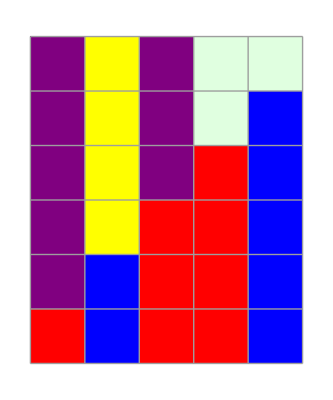

```mathematica
(*
Práctica 2 parte 2
Alumnos:
Dan Anitei
Vicente Gras Mas

*)


(* Ejercicio1: Implemente un módulo en Mathematica que, tomando como entrada un AFD proporcione
como salida un AC unidireccional unidimensional que acepte el mismo lenguaje que el AFD
mediante entrada paralela. *)
Ej1[A_List]:=Module[{f,sfin,s,i,j},
f = A[[3]];
sfin = A[[5]];
s = Union[A[[1]],A[[2]]];
(* para todo estado q,p de A[[1]], añadimos f(q,p)=p *)
For[i = 1, i≤ Length[A[[1]]],i++,
For[j = 1, j≤Length[A[[1]]],j++,
 AppendTo[f,{A[[1,i]],A[[1,j]],A[[1,j]]}];
];
];
(* para todo simbolo a,b de A[[2]], añadimos f(a,b)=b *)
For[i = 1, i≤ Length[A[[2]]],i++,
For[j = 1, j≤Length[A[[2]]],j++,
 AppendTo[f,{A[[2,i]],A[[2,j]],A[[2,j]]}];
];
];
(* retorna un AC unidireccional unidimensional representado como una tupla(S,f,S+) creada con una lista de listas*)
Return[{s,f,sfin}]
]

(* Autómata finíto determinista *)
Ej1[{{q,p,r},{a,b},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},q,{r}}]


(* Ejercicio2: Implemente un módulo Mathematica que,tomando como entrada una cadena arbitraria,un AC que reconoce un lenguaje mediante entrada paralela en tiempo real y un estado de
frontera q ϵ S,proporcione como salida True si el AC acepta la cadena y False en caso contrario. *)

Ej2[w_,AC_,q_]:=Module[{f,i,pal,trans},
f=AC[[2]];
pal =w;
(* Hacemos la primera configuración *)
trans=Cases[f,{q,pal[[1]],_}];
If[Length[trans]>0,
pal[[1]]=trans[[1,3]];,
Return[False];
];
(* Para los demás simbolos de 'w' miramos el vecindario {-1,0} *)
For[i=2,i≤Length[pal],i++,
trans=Cases[f,{pal[[i-1]],pal[[i]],_}];
If[Length[trans]>0,
pal[[i]]=trans[[1,3]];,
Return[False];
];
];
(* Si la celula de salida ha entrado en estado de aceptación, devuelve True y False en caso contrario *)
If[MemberQ[AC[[3]],Last[pal]],
Return[True],
Return[False]
];
]
(* w= 'abaab', AC=ejemplo transparencia, q, devuelve True *)
Ej2[{a,b,a,a,b},{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r},{q,q,q},{q,p,p},{q,r,r},{p,q,q},{p,p,p},{p,r,r},{r,q,q},{r,p,p},{r,r,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b}},{r}},q]
(* w= 'ababa', AC=ejemplo transparencia, q, devuelve False *)
Ej2[{a,b,a,b,a},{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r},{q,q,q},{q,p,p},{q,r,r},{p,q,q},{p,p,p},{p,r,r},{r,q,q},{r,p,p},{r,r,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b}},{r}},q]


(* Ejercicio3: Proporcione una construcción formal para obtener a partir de un AFD,un AC equivalente
unidimensional bidireccional (vecindario {-1,0,1}) con entrada paralela.Implemente un
módulo en Mathematica que lleve a cabo la construcción propuesta. *)
Ej3[A_List]:=Module[{ac,f,i,j,aux,vecDer},
ac = Ej1[A];
f={};
(* para todas las transiciones definidas en 'ac' hay que añadir el vecino derecho, vecindario {-1,0,1} *)
For[i = 1, i≤ Length[ac[[2]]],i++,
For[j = 1, j≤Length[ac[[1]]],j++,
 AppendTo[f,{ac[[2,i,1]],ac[[2,i,2]],ac[[1,j]],ac[[2,i,3]]}];
];
];
ac[[2]]=f;
(* retorna un AC unidireccional unidimensional representado como una tupla(S,f,S+) creada con una lista de listas*)
Return[ac];
]
Ej3[{{q,p,r},{a,b},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r}},q,{r}}]


(* Ejercicio4: Implemente un módulo Mathematica que muestre la secuencia de computación que se
lleva a cabo en el módulo propuesto en la actividad (2) mediante un diagrama espacio-temporal.(Nota:Utilice las funciones ArrayPlot y ListAnimate explicados en la práctica de Fundamentos Básicos) *)
Ej4[w_,AC_,q_]:=Module[{f,pal,trans,i,diag,lista},
f=AC[[2]];
pal =w;
diag={pal};
lista={pal};
(* Hacemos la primera configuración *)
trans=Cases[f,{q,pal[[1]],_}];
If[Length[trans]>0,
pal[[1]]=trans[[1,3]];
];
PrependTo[diag,pal];
AppendTo[lista,pal];
(* Para los demás simbolos de 'w' miramos el vecindario {-1,0} *)
For[i=2,i≤Length[pal],i++,
trans=Cases[f,{pal[[i-1]],pal[[i]],_}];
If[Length[trans]>0,
pal[[i]]=trans[[1,3]];
PrependTo[diag,pal];
AppendTo[lista,pal];
];
];
(* Secuencia de computación *)
ListAnimate[lista]
(*Diagrama espacio-temporal*)
ArrayPlot[diag,ColorRules->{a->Red,b-> Blue, p-> Purple,q->Yellow,r->LightGreen},Mesh->True]
]

Ej4[{a,b,a,a,b},{{a,b,p,q,r},{{q,a,p},{q,b,r},{p,a,r},{p,b,q},{r,a,r},{r,b,r},{q,q,q},{q,p,p},{q,r,r},{p,q,q},{p,p,p},{p,r,r},{r,q,q},{r,p,p},{r,r,r},{a,a,a},{a,b,b},{b,a,a},{b,b,b}},{r}},q]
```